# Projekt 1 - Konvolution

## IX1501

## Uppgift 1: Konvolution

Den första uppgiften består av fyra deluppgifter som inkluderar ett tärningsspel med chansen att vinna en Teddy.
Tärningsspelet består av fem olika tärningar (d4, d6, d8, d12 och d20 tärningar). Om summan av alla tärningar, X, har ett värde under 10 eller över 45, så vinner man Teddyn.

De fyra deluppgifterna är följande:
Finn den exakta probabilitetsfunktionen av summan.
Bestäm den exakta probabiliteten att vinna Teddyn. Ge även svaret med flyttalsvärde.
Bestäm den förväntade investeringen som krävs för att vinna Teddyn.
Vad är probabiliteten att vinna en Teddy om man spelar tjugo gånger?

## Finn den exakta probabilitetsfunktionen av summan

Sannolikheten för varje tärning:

```mathematica
Ppf1[k_]:=Piecewise[{{1/4, 1≤ k ≤ 4}},0  (* default *)];
Ppf2[k_]:=Piecewise[{{1/6, 1≤ k ≤ 6}},0  (* default *)];
Ppf3[k_]:=Piecewise[{{1/8, 1≤ k ≤ 8}},0  (* default *)];
Ppf4[k_]:=Piecewise[{{1/12, 1≤ k ≤ 12}},0  (* default *)];
Ppf5[k_]:=Piecewise[{{1/20, 1≤ k ≤ 20}},0  (* default *)];
```

Sannolikheterna för summorna av tärningarna kan beräknas genom DiscreteConvolve:

```mathematica
x1[s_]=DiscreteConvolve[Ppf1[k],Ppf2[k],k,s];
x2[s_]=DiscreteConvolve[x1[k],Ppf3[k],k,s];
x3[s_]=DiscreteConvolve[x2[k],Ppf4[k],k,s];
x4[s_]=DiscreteConvolve[x3[k],Ppf5[k],k,s];
```

Vi kan även plotta sannolikheten för varje summa:

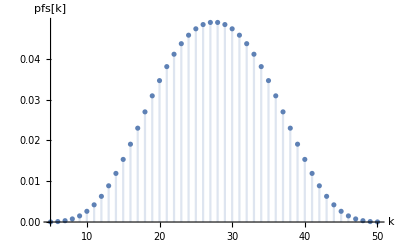

```mathematica
plotDiscrete =DiscretePlot[x4[k],{k,5,50},AxesLabel->{"k","pfs[k]"}]
```

## Sannolikheten att vinna en teddy

För att beräkna sannolikheten att vinna så tar vi sannolikheterna att vinna och adderar de:

```mathematica
p = Sum[x4[k], {k,0,10}] + Sum[x4[k], {k,45,50}] //N
```

0.0106771

## Förväntade investeringen för att vinna Teddyn

Vi kan jämföra denna uppgift med en vanlig tärning. Alla sidor har 1/6 chans att dyka upp. Därmed kan man förvänta sig att man får sin önskade sida efter sex kast. Matematiskt kan man skriva det som 1/1/6 = 6.
Med samma logik kan man beräkna investeringen som krävs för att vinna Teddyn. Det finns en  41/3840 chans att vinna Teddyn. Därmed kräv det 1/41/3840 antal kast för att vinna Teddyn.

1/41/3840=3840/41=93.6585≈94 kast

Eftersom varje kast kostar 2 Euro så blir den förväntade investeringen 188 euro.

## Vinna en teddy (minst en gång) efter 20 spelomgångar

Genom att ta den sammanlagda summan av alla utfall (100% eller 1) och subtrahera förlustchansen för 20 kast så kan vi beräkna vinstchansen för 20 kast: 1-((1- p)^20) =0.1932...
Vilket kan tolkas som ~20% att vinna teddyn om man spelar 20 gånger, vilket passar in på vår tidigare beräkning i den föregående uppgiften, då ett kast har en cirka 1% chans att vinna Teddyn.

## Uppgift 2: Normalfördelning

I denna uppgift ska vi fortsätta med uppgift 1 men vi ska använda normalfördelning för att svara på deluppgifterna nedan:

Bestäm väntevärdet och standardavvikelsern för fördelningen i Teddy-fallet.

Bestäm sannolikheten för teddypriset med normal distribution.

Jämför och kommentera resultaten mellan första och andra uppgiften.

## Väntevärde och standardavvikelse

Väntevärdet för en diskret stokastisk variable X defineras som:

μ = E(X) =∑_(∀x) x pf_X(x)

Där s.v. X är summan av ett kast och pf_X(x) är sannolikheten för att få summan X.
Med formeln fick vi väntevärdet  μ = 55/2 = 27.5  

För att få ut standardavvikelse σ måste vi först få ut variansen  σ^2:

σ^2 = E((X -μ)^2) = 
E(X^2-2Xμ + μ^2) = E(X^2) - 2E(X)μ + μ^2 = 
E(X^2) - μ^2

E(X^2) = ∑_(∀x) x^2 pf_X(x) =4865/6 ≃ 810.833

μ^2 = (27.5)^2 = 756.25

σ^2 = 4865/6  - 756.25 = 655/12  ≃ 54.5833

Om man tar roten ur variansen så får man standardavvikelsen:

σ =  √(σ^2)=  √(E(X^2) - μ^2)
σ = √(655/12)= 7.38805

## Väntevärde och standardavvikelse (I Mathematica)

Mathematica har inbyggda funktioner för att kunna räkna ut väntevärdet och standardavvikelsen

```mathematica
Δk=1;
```

```mathematica
𝒟=ProbabilityDistribution[x4[k],{k,5,50,Δk}];
```

```mathematica
μ = Mean[𝒟]
```

55/2

```mathematica
σ = StandardDeviation[𝒟] //N
```

7.38805

## Sannolikheten för teddypriset med normalfördelning

Vi kan få ut normalfördelningen genom att mata in μ och σ i  Mathematicas normalfördelnings funktion.

```mathematica
n=NormalDistribution[μ,σ];
```

Nu kan vi få ut  cdf_x(x) och pdf_t(t) och plotta dem.

```mathematica
PDF[n,x]//TraditionalForm
CDF[n,x]//TraditionalForm
```

√(6/(655 π)) ⅇ^(-6/655 (x-55/2)^2)

1/2 erfc(√(6/655) (55/2-x))

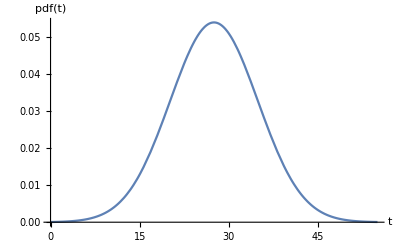

```mathematica
plotNormalD = Plot[PDF[n,x],{x,0,55},PlotRange->All,
AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}]
```

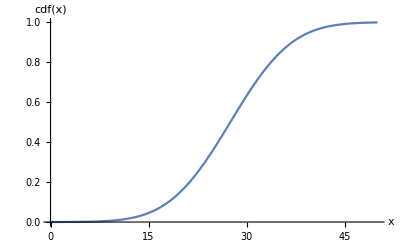

```mathematica
Plot[CDF[n,x],{x,0,50},PlotRange->All,
AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}]
```

Sannolikhet att vinna en teddy:

```mathematica
CDF[n,10]-CDF[n,5]+CDF[n,50]-CDF[n,45] //N
```

0.015528

## Normalfördelningen jämfört med första uppgiften

Jämförelse mellan normalfördelningen och discketa fördelningen från första uppgiften.

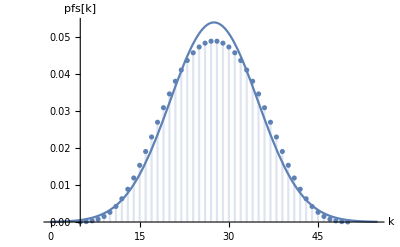

```mathematica
Show[plotDiscrete, plotNormalD, PlotRange -> Automatic]
```